表达式及其结构

我们现在已经看到了 Wolfram 语言中存在的各种东西：列表、图形、纯函数等等。现在我们准备讨论一下关于 Wolfram 语言的一个非常基本的事实：这些东西归根结底都是以相同的基本方式构建的，事实上，该语言处理的所有东西都是如此。一切都是符号表达式。

符号表达式是表示结构的一种非常普遍的方式，可能有与该结构相关的意义。f[x,y] 是符号表达式的一个简单例子。就其本身而言，这个符号表达式并没有任何特定的意义，如果你把它输入 Wolfram 语言，它就会原原本本地返回。

f[x,y] 是一个符号表达式，没有附加任何特殊的含义：

```mathematica
f[x,y]
```

f[x,y]

{x,y,z} 是另一个符号表达式。在内部，它是 List[x,y,z]，但它被显示为 {x,y,z}。

符号表达式 List[x,y,z] 显示为 {x,y,z}：

```mathematica
List[x,y,z]
```

{x,y,z}

符号表达式经常都是嵌套的：

```mathematica
List[List[a,b],List[c,d]]
```

{{a,b},{c,d}}

FullForm 将向你显示任意符号表达式的内部形式。

```mathematica
FullForm[{{a,b},{c,d}}]
```

List[List[a,b],List[c,d]]

Graphics[Circle[{0,0}]] 是另一个符号表达式，它恰好显示为一个圆的图形。FullForm 显示了它的内部结构。

这个符号表达式显示为一个圆形：

```mathematica
Graphics[Circle[{0,0}]]
```

-Graphics-

FullForm 显示了它的底层符号表达式结构：

```mathematica
FullForm[-Graphics-]
```

Graphics[Circle[List[0,0]]]

符号表达式往往不仅仅是以特殊的方式显示，它们实际上是通过计算来给出结果。

一个符号表达式，计算后给出一个结果：

```mathematica
Plus[2,2]
```

4

列表中的元素被计算，但列表本身保持符号化：

```mathematica
{Plus[3,3],Times[3,3],Power[3,3]}
```

{6,9,27}

下面是该列表的符号表达式结构：

```mathematica
{Plus[3,3],Times[3,3],Power[3,3]}//FullForm
```

List[6,9,27]

这只是一个符号表达式，刚好可以进行计算：

```mathematica
Blur[-Graphics-,5]
```

-Graphics-

你可以这样写：

```mathematica
Blur[Graphics[Circle[{0,0}]],5]
```

-Graphics-

构成符号表达式的最小单元是什么？它们被称为原子(取自物理材料的最小单元)。原子的主要种类是数字、字符串和符号。

像 x、y、f、Plus、Graphics 以及 Table 这些东西都是符号。每个符号都有一个独特的名字，有时它也会有一个附加的含义。有时它与计算有关。有时它只是定义一个结构的一部分，然后可以用在其他函数中。但它不一定要有这些东西，它唯一必须的是一个名字。

Wolfram 语言的一个决定性的特征是，它可以纯粹地将符号作为符号 — 符号性地处理，而不需要对它们进行计算，比如说数字。

在 Wolfram 语言中，x 可以只是 x，而不用计算为任何对象：

```mathematica
x
```

x

x 不进行计算，但加法仍在进行，这是根据代数规律进行的：

```mathematica
x+x+x+2y+y+x
```

4 x+3 y

给定像 x、y 还有 f 这样的符号，可以使用它们建立起无限多的表达式。比如 f[x]、f[y] 以及 f[x,y]。还有 f[f[x]] 或者 f[x,f[x,y]]，或者，就这个问题而言，还有 x[x][y,f[x]] 或其他。

一般来说，每个表达式都对应于一棵树，其最终的“叶子”是原子。你可以使用 TreeForm 将表达式显示为一棵树。

以树形式显示的表达式：

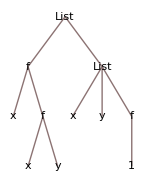

```mathematica
TreeForm[{f[x,f[x,y]],{x,y,f[1]}}]
```

这是一个以树形式显示的图形表达式：

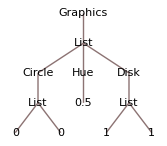

```mathematica
TreeForm[Graphics[{Circle[{0,0}],Hue[0.5],Disk[{1,1}]}]]
```

因为表达式最终有一个非常统一的结构，Wolfram 语言中的操作也以非常统一的方式对它们进行操作。

例如，任何表达式都有各个部分，就像列表一样，你可以用 [[...]] 来提取它们。

这相当于 {x,y,z}[[2]]，它将取出列表中的第二个元素：

```mathematica
List[x,y,z][[2]]
```

y

对于这个表达式，取出各个部分的工作方式完全相同：

```mathematica
f[x,y,z][[2]]
```

y

这将从图形中提取出圆：

```mathematica
Graphics[Circle[{0,0}]][[1]]
```

Circle[{0,0}]

这会继续下去，提取出其中心坐标：

```mathematica
Graphics[Circle[{0,0}]][[1,1]]
```

{0,0}

这样做的效果是完全一样的：

```mathematica
-Graphics-[[1,1]]
```

{0,0}

在 f[x,y]中，f 被称为表达式的标头，x 和 y 被称为参数。函数 Head 可以获取表达式的标头。

列表的标头是 List：

```mathematica
Head[{x,y,z}]
```

List

表达式的每个部分都有一个标头，甚至是原子也有。

整数的标头是 Integer：

```mathematica
Head[1234]
```

Integer

一个近似实数的标头是 Real：

```mathematica
Head[12.45]
```

Real

字符串的标头是 String：

```mathematica
Head["hello"]
```

String

即使是符号也有一个标头：Symbol。

```mathematica
Head[x]
```

Symbol

在模式中，你可以要求匹配具有特定标头的表达式。_Integer 表示任何整数，_String 表示任何字符串，以此类推。

_Integer 是只匹配标头为 Integer 的对象一个模式：

```mathematica
Cases[{x,y,3,4,z,6,7},_Integer]
```

{3,4,6,7}

命名的模式也可以有指定的标头：

```mathematica
Cases[{99,x,y,z,101,102},n_Integer->{n,n}]
```

{{99,99},{101,101},{102,102}}

在使用 Wolfram 语言的过程中，你所看到的大部分标头都是符号。但在一些重要的情况下，会有更复杂的标头。其中一种情况是纯函数，当你应用一个纯函数时，纯函数就会作为标头出现。

下面是一个纯函数的完整形式(# 是 Slot[1])：

```mathematica
FullForm[#^2&]
```

Function[Power[Slot[1],2]]

当你应用纯函数时，它就会作为标头出现：

```mathematica
Function[Power[Slot[1],2]] [1000]
```

1000000

随着你在 Wolfram 语言编程中变得越来越复杂，你会遇到越来越多的复杂头部的例子。事实上，我们已经讨论过的许多函数都有运算符形式，它们作为标头出现，以这种方式使用它们会带来非常强大的功能，并且代码也很优雅。

这里 Select 作为标头出现：

```mathematica
Select[#>4&][{1,2.2,3,4.5,5,6,7.5,8}]
```

{4.5,5,6,7.5,8}

这里 Cases 与 Select 均作为标头出现：

```mathematica
Cases[_Integer]@Select[#>4&]@{1,2.2,3,4.5,5,6,7.5,8}
```

{5,6,8}

我们所看到的对列表的所有基本结构操作对任意表达式都适用。

Length 并不关心表达式的标头是什么，它只是计算参数个数：

```mathematica
Length[f[x,y,z]]
```

3

/@ 也不关心表达式的标头，它只是将一个函数应用于所有参数：

```mathematica
f/@g[x,y,z]
```

g[f[x],f[y],f[z]]

由于有很多函数可以生成列表，所以即使最终需要用其他函数来替换列表，以列表的形式来建立结构往往也很方便。

@@ 可以有效地将列表的标头替换为 f：

```mathematica
f@@{x,y,z}
```

f[x,y,z]

这将生成 Plus[1,1,1,1]，然后进行计算:

```mathematica
Plus@@{1,1,1,1}
```

4

这将把一个列表转换为一个规则：

```mathematica
#1->#2&@@{x,y}
```

x→y

这里有一个更简单的形式，没有明确使用纯函数：

```mathematica
Rule@@{x,y}
```

x→y

一个意外常见的情况是有一个列表的列表，并想用一些函数来替换内层的列表。用 @@ 和 /@ 可以完成这一点。但是 @@@ 提供了一个方便直接的方式。

将内层的列表替换为 f：

```mathematica
f@@@{{1,2,3},{4,5,6}}
```

{f[1,2,3],f[4,5,6]}

将内层列表转换为规则：

```mathematica
Rule@@@{{1,10},{2,20},{3,30}}
```

{1→10,2→20,3→30}

下面是一个例子，说明 @@@ 如何帮助使用成对对象的列表(list of pairs)来创建一个图。

这将生成一个成对字符的列表:

```mathematica
Partition[Characters["antidisestablishmentarianism"],2,1]
```

{{a,n},{n,t},{t,i},{i,d},{d,i},{i,s},{s,e},{e,s},{s,t},{t,a},{a,b},{b,l},{l,i},{i,s},{s,h},{h,m},{m,e},{e,n},{n,t},{t,a},{a,r},{r,i},{i,a},{a,n},{n,i},{i,s},{s,m}}

将它转换为规则列表：

```mathematica
Rule@@@Partition[Characters["antidisestablishmentarianism"],2,1]
```

{a→n,n→t,t→i,i→d,d→i,i→s,s→e,e→s,s→t,t→a,a→b,b→l,l→i,i→s,s→h,h→m,m→e,e→n,n→t,t→a,a→r,r→i,i→a,a→n,n→i,i→s,s→m}

创建一个过渡图，显示字母如何相互接续：

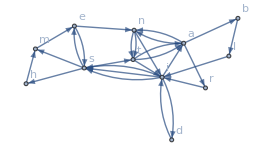

```mathematica
Graph[Rule@@@Partition[Characters["antidisestablishmentarianism"],2,1],VertexLabels->All]
```

词汇

FullForm[expr] |   | 显示完整的内部格式
TreeForm[expr] |   | 显示树结构
Head[expr] |   | 提取表达式的标头
_head |   | 匹配任意带有特定标头的表达式
f@@list |   | 将 list 的标头替换为 f
f@@@{list_1,list_2, ...} |   | 将 list_1、list_2 ... 的标头替换为 f

"共有 8 道习题" | "开始练习 »"

找出 ListPlot 的输出的标头。»

| 期望输出： |  
  | Graphics |

使用 @@ 来计算 100 以内的整数相乘的结果。»

| 期望输出： |  
  | 93326215443944152681699238856266700490715968264381621468592963895217599993229915608941463976156518286253697920827223758251185210916864000000000000000000000000 |

使用 @@@ 和 Tuples 来生成 {f[a,a],f[a,b],f[b,a],f[b,b]}。»

| 期望输出： |  
  | {f[a,a],f[a,b],f[b,a],f[b,b]} |

为从 x 开始连续应用 #^#& 4 次的结果创建一个树形列表。»

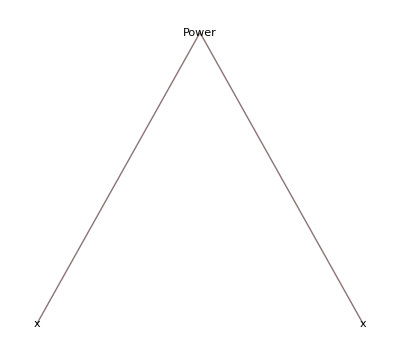
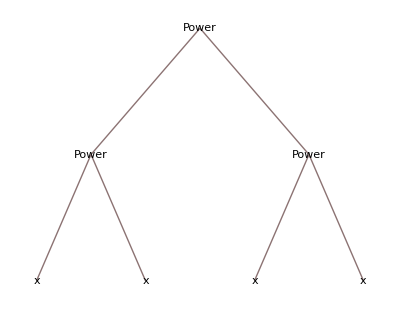
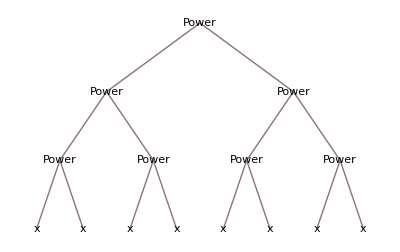
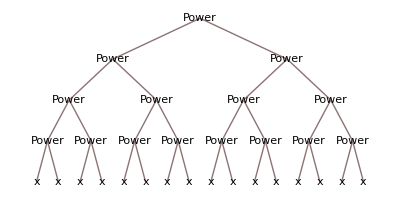
| 期望输出： |  
  | {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-} |

找出 i^2/(j^2+1) 为整数的情况，其中 i 和 j 最大为 20。»

| 期望输出： |  
  | {2,5,8,10,17,18,20,32,40,45,50,72,80,98,128,162,200} |

创建一个连接 Table[Mod[n^2+n,100],{n,100}] 中连续的成对数字的图。»

| 期望输出： |  
  | -Graphics- |

生成一个图，显示在维基百科上关于计算机的文章的前 200 个单词中，哪个词可以跟在哪个后面。»

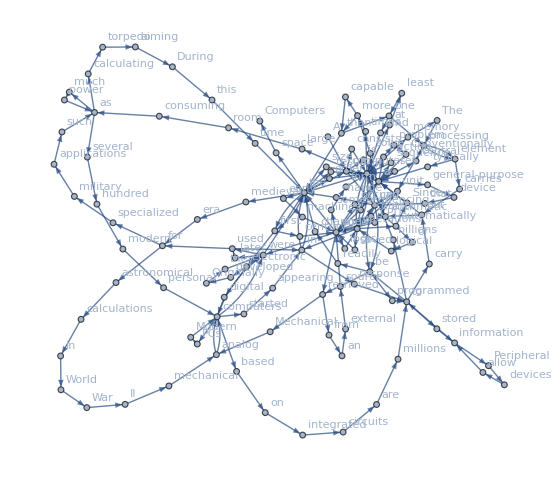
| 期望输出示例： |  
  | -Graphics- |

为 f@@#&/@{{1,2},{7,2},{5,4}} 找一个更简单的形式。»

| 期望输出示例： |  
  | {f[1,2],f[7,2],f[5,4]} |

问&答

@@ 和 @@@ 在内部是如何解释的？

f@@expr 就是 Apply[f,expr]。f@@@expr 就是 Apply[f,expr,{1}]。它们通常读作“双 at”和“三 at”。

Wolfram 语言中的所有表达式都是树吗？

在结构层面上，是的。不过，当有变量赋值时(详见第 38 节)，它们的行为更像是有向图。当然，我们也可以用 Graph 来表示任何图，作为 Wolfram 语言中的表达式。

技术笔记

符号语言的基本概念直接来自于 20 世纪 30 年代及以前的数理逻辑工作，但除了在 Wolfram 语言中，它在实践中被实现的情况非常少。

Wolfram 语言表达式有点像 XML 表达式(并且可以互相转换)。但与 XML 表达式不同的是，Wolfram 语言表达式可以进行计算，从而自动改变其结构。

像 Select[f] 这样应用于表达式的对象，通常与数学中的运算符相似，被称为运算符形式。使用 Select[f][expr] 而不是 Select[expr,f] 通常被称为 currying，这是根据一位名叫 Haskell Curry 的逻辑学家的名字来命名的。

像 x 这样的符号可以用来表示代数变量或“未知数”。这是在 Wolfram 语言中进行许多种数学运算的核心。

LeafCount 将给出表达式树的叶子上的原子总数。ByteCount 将给出存储表达式所需的字节数。

探索更多

Wolfram 语言中的表达式指南 »